```mathematica
(*1：每题5分，第一个：表达、画图各1分；第二个：求出3个解和表达给4分，画图给1分*)
(*直接求，不用提取解的命令[[1,1,2]]等也对*)
```

-3/2

-7/2

√(29/2)

-π+ArcTan[7/3]

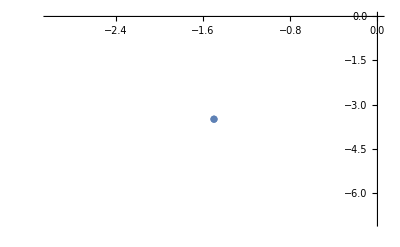

```mathematica
Clear["`*"]
z=2/I-3*I/(1+I);
Re[z]
Im[z]
Abs[z]
Arg[z]
ListPlot[{{Re[z],Im[z]}}]
```

{{z→2},{z→-2 (-1)^(1/3)},{z→2 (-1)^(2/3)}}

2

-2 (-1)^(1/3)

2 (-1)^(2/3)

2

0

2

0

-1

-√3

2

-(2 π)/3

-1

√3

2

(2 π)/3

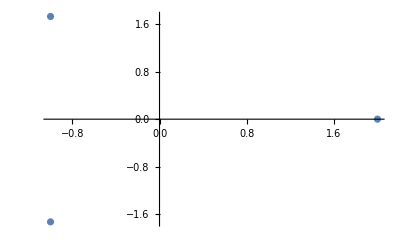

```mathematica
Clear["`*"]
a=Solve[z^3==8,z]
z1=a[[1,1,2]]
z2=a[[2,1,2]]
z3=a[[3,1,2]]
Re[z1]
Im[z1]
Abs[z1]
Arg[z1]
Re[z2]
Im[z2]
Abs[z2]
Arg[z2]
Re[z3]
Im[z3]
Abs[z3]
Arg[z3]
ListPlot[{{Re[z1],Im[z1]},{Re[z2],Im[z2]},{Re[z3],Im[z3]}}]
```

```mathematica
(*2：只对一题给3分（两个变换只对一个给2分），对两题给7分，全对给10分*)
(*傅里叶变换、逆变换时乘不乘以系数根号2Pi都给满分*)
Clear["`*"]
f1[t_]:=Exp[-t^2];
FourierTransform[f1[t],t,w]
LaplaceTransform[f1[t],t,s]
f2[t_]:=UnitBox[t/2];
FourierTransform[f2[t],t,w]
LaplaceTransform[f2[t],t,s]
f3[t_]:=Exp[-t]*UnitStep[t];
FourierTransform[f3[t],t,w]
LaplaceTransform[f3[t],t,s]
```

```mathematica
(*3:先展开，然后复制出来画图也是对的；
求出一个级数给3分，画出了图给1分*)
```

1/3-x/9+x^2/27-x^3/81

1/3-x/9+x^2/27-x^3/81+x^4/243-x^5/729

1/3-x/9+x^2/27-x^3/81+x^4/243-x^5/729+x^6/2187-x^7/6561+x^8/19683-x^9/59049

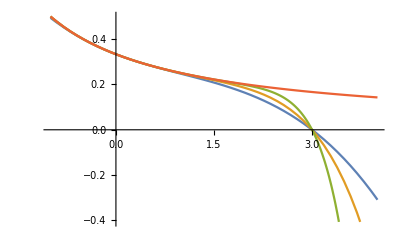

```mathematica
Clear["`*"]
f3=Normal[Series[1/(x+3),{x,0,3}]]
f5=Series[1/(x+3),{x,0,5}]//Normal
f9=Series[1/(x+3),{x,0,9}]//Normal
Plot[{f3,f5,f9,1/(x+3)},{x,-1,4}]
```

((0.+0.797885 ⅈ)-(0.+0.797885 ⅈ) Cos[w]+0.797885 Sin[w])/w-0.398942 ⅇ^((0.-0.5 ⅈ) w) Sinc[w/2]

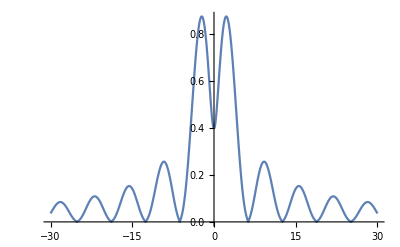

```mathematica
(*4：除了用基本函数表达外，用分段函数表示f[x]也是对的；
写出函数表达给3分，求出了傅里叶变换给7分，画出了图给10分*)
(*傅里叶变换、逆变换时乘不乘以系数根号2Pi都给满分*)
f[x_]:=2*UnitBox[x-0.5]-UnitBox[x+0.5]
g=FourierTransform[f[x],x,w]
Plot[Abs[g],{w,-30,30},PlotRange->All]
```

2 ⅇ^-s Sinh[s] UnitStep[s]

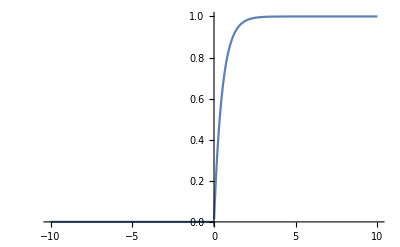

(ⅈ ((ⅈ √(2/π))/w+√(2 π) DiracDelta[w]))/(√(2 π) (2 ⅈ+w))

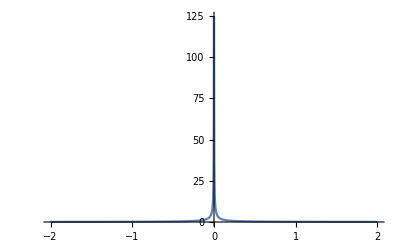

```mathematica
(*5：除了用基本函数表达外，用分段函数表示f1[t]、f2[t]也是对的；
求出卷积给5分，求出了频谱并画图给10分*)
(*傅里叶变换、逆变换时乘不乘以系数根号2Pi都给满分*)
Clear["`*"]
f1[t_]:=2*UnitStep[t];
f2[t_]:=Exp[-2*t]*UnitStep[t];
Conv=Convolve[f1[t],f2[t],t,s]
Plot[Conv,{s,-10,10}]
g1=FourierTransform[f1[t],t,w];
g2=FourierTransform[f2[t],t,w];
G=g1*g2
Plot[Abs[G],{w,-2,2},PlotRange->All]
```

1/45 ⅇ^(-12 t) (76-85 ⅇ^(9 t)+54 ⅇ^(10 t)) UnitStep[t]

2 (-1+ⅇ^-t/2+ⅇ^t/2-t^2/2) UnitStep[t]

2/45 (Piecewise[{{-(19 ⅇ^(-12 p))/61776+(85 ⅇ^(-3 p))/216-(9 ⅇ^(-2 p))/4+(405 ⅇ^-p)/44+(135 ⅇ^p)/104-5/48 (83-44 p+24 p^2), p≥0}, {0, True}}])

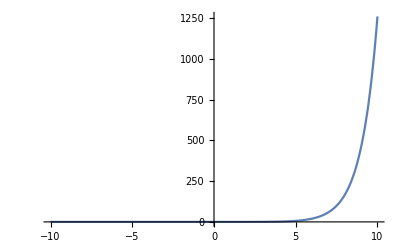

```mathematica
(*6：如果逆变换后没乘阶跃函数会计算不出来，但是不用阶跃函数，用分段函数表示出来了也可以*)
(*只求出逆变换给4分（单纯求出逆变换，没有乘上UnitStep[t]同样给分），求出卷积给8分*)
Clear["`*"]
F1[s_]:=(s^2+8)/((s^2+5*s+6)*(s+12));
F2[s_]:=2/(s^3*(s^2-1));
f1=InverseLaplaceTransform[F1[s],s,t]*UnitStep[t]
f2=InverseLaplaceTransform[F2[s],s,t]*UnitStep[t]
G=Convolve[f1,f2,t,p]
Plot[G,{p,-10,10},PlotRange->All]
```

1/2 ⅇ^-t t^3

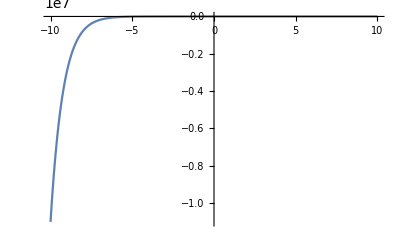

```mathematica
(*7：[[1,1,2]]为提取解，自行复制出来也行；
只求出了解给8分，画图2分*)
Clear["`*"]
DSolve[{y'''[t]+3*y''[t]+3*y'[t]+y[t]==3*Exp[-t],y''[0]==0,y'[0]==0,y[0]==0},y[t],t][[1,1,2]]
Plot[%,{t,-10,10},PlotRange->All]
```

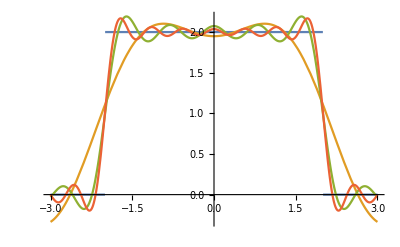

```mathematica
(*8：函数表达、级数展开（3个）和画图各2分*)
Clear["`*"]
f[t_]:=2*UnitBox[t/4];
g2=FourierSeries[f[t],t,2];
g7=FourierSeries[f[t],t,7];
g11=FourierSeries[f[t],t,11];
Plot[{f[t],g2,g7,g11},{t,-3,3}]
```

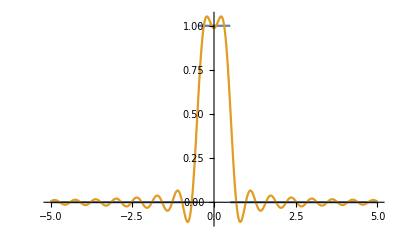

```mathematica
(*9：函数表达、傅里叶变换、截取频谱、逆变换、画图各2分；只画出了原信号图和求傅里叶变换给5分*)
(*傅里叶变换、逆变换时乘不乘以系数根号2Pi都给满分；频谱截取宽度w0自行设定即可*)
Clear["`*"]
T0=1;
w0=20;
f[t_]:=UnitBox[t/T0];
gw=FourierTransform[f[t],t,w];
gw1=gw*UnitBox[w/w0];
gt=InverseFourierTransform[gw1,w,t];
Plot[{f[t],gt},{t,-5,5},PlotRange->All]
```

```mathematica
(*10：两个各占5分，只求出了解没画图，一个解给3分；加了边界条件u[-10,z]==u[10,z]也是对的*)
Clear["`*"]
p=0;
solution=NDSolve[{I*D[u[x,z],z]+0.5*D[u[x,z],x,x]==0,u[x,0]==Exp[-x^2]*Exp[-I*p*x^2]},u[x,z],{x,-10,10},{z,0,3}]
Plot3D[Evaluate[Abs[u[x,z]]/.First[solution]],{x,-10,10},{z,0,3},PlotRange->Full]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

{{u[x,z]→InterpolatingFunction[…][x,z]}}

-Graphics3D-

```mathematica
Clear["`*"]
p=1;
solution=NDSolve[{I*D[u[x,z],z]+0.5*D[u[x,z],x,x]==0,u[x,0]==Exp[-x^2]*Exp[-I*p*x^2]},u[x,z],{x,-10,10},{z,0,3}]
Plot3D[Evaluate[Abs[u[x,z]]/.First[solution]],{x,-10,10},{z,0,3},PlotRange->Full]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

{{u[x,z]→InterpolatingFunction[…][x,z]}}

-Graphics3D-

```mathematica
(*附加：10：用非数值求解的参考答案，但是求对了也只能给4分，题目要求是数值求解，没有求对就不给分了*)
```

```mathematica
Clear["`*"]
p=0;
solution=DSolve[{I*D[u[x,z],z]+0.5*D[u[x,z],x,x]==0,u[x,0]==Exp[-x^2]*Exp[-I*p*x^2]},u[x,z],{x,z}][[1,1,2]]
Plot3D[Abs[solution],{x,-10,10},{z,0,3}]
```

(0.707107 ⅇ^(-x^2/(1.+(0.+2. ⅈ) z)))/(√(0.5+(0.+1. ⅈ) z))

-Graphics3D-

```mathematica
Clear["`*"]
p=1;
solution=DSolve[{I*D[u[x,z],z]+0.5*D[u[x,z],x,x]==0,u[x,0]==Exp[-x^2]*Exp[-I*p*x^2]},u[x,z],{x,z}][[1,1,2]]
Plot3D[Abs[solution],{x,-10,10},{z,0,3}]
```

((0.549342-0.227545 ⅈ) ⅇ^(-x^2/((0.5-0.5 ⅈ)+(0.+2. ⅈ) z)))/(√((0.25-0.25 ⅈ)+(0.+1. ⅈ) z))

-Graphics3D-